```mathematica
Quicksort={{100,1},{1000,1},{10000,5},{100000,113},{1000000,207},{10000000,2701},{100000000,54304}};
MergeSort={{100,0},{1000,1},{10000,5},{100000,19},{1000000,437},{10000000,5152},{100000000,58632}};
```

```mathematica
InsertionSort={{100,8},{1000,10},{10000,211},{100000,15157}};
```

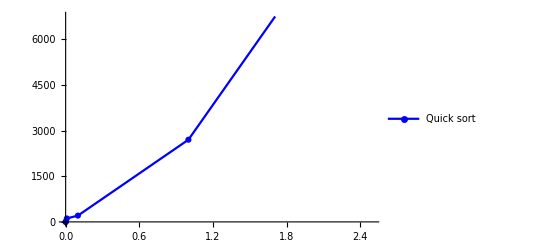

```mathematica
quickplot = ListLinePlot[Quicksort ,PlotLegends->{"Quick sort"}, PlotMarkers->Automatic, PlotStyle->Blue]
```

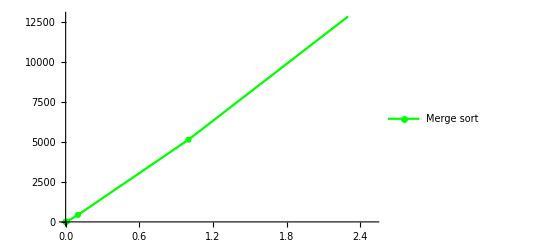

```mathematica
mergeplot =ListLinePlot[MergeSort,PlotLegends->{"Merge sort"}, PlotMarkers->Automatic, PlotStyle->Green]
```

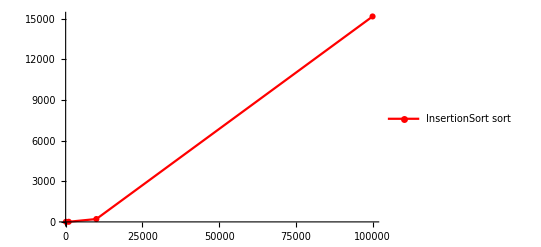

```mathematica
Insertionplot = ListLinePlot[InsertionSort,PlotLegends->{"InsertionSort sort"}, PlotMarkers->Automatic, PlotStyle->Red]
```

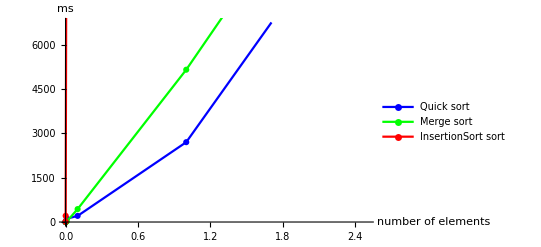

```mathematica
Show[quickplot,mergeplot,Insertionplot, AxesLabel->{"number of elements", "ms"}]
```